```mathematica
Clear["Global`*"]
```

```mathematica
Needs["Developer`"]
nStage=5;
nOrder=4;
a2={1/4}//N//ToPackedArray;
a3={3/32,9/32}//N//ToPackedArray;
a4={1932/2197,-7200/2197,7296/2197}//N//ToPackedArray;
a5={439/216,-8,3680/513,-845/4104}//N//ToPackedArray;
a6={-8/27,2,-3544/2565,1859/4104,-11/40}//N//ToPackedArray;
c={0,1/4,3/8,12/13,1,1/2}//N//ToPackedArray;
b4={25/216,0,1408/2565,2197/4104,-1/5}//N//ToPackedArray;
b5={16/135,0,6656/12825,28561/56430,-9/50,2/55}//N//ToPackedArray;
```

3.13706×10^-6

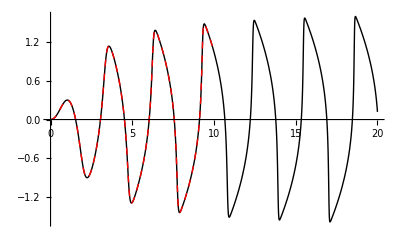

0. | 0.
0.01 | 0.0000424439
0.02 | 0.000171126
0.03 | 0.000388054
0.04 | 0.000695153
0.05 | 0.00109421
0.06 | 0.00158691
0.07 | 0.00217484
0.08 | 0.00285947
0.09 | 0.00364216
0.1 | 0.00452416
0.11 | 0.00550661
0.12 | 0.00659052
0.13 | 0.00777683
0.14 | 0.00906627
0.15 | 0.0104595
0.16 | 0.0119572
0.17 | 0.0135597
0.18 | 0.0152673
0.19 | 0.0170802
0.2 | 0.0189985
0.21 | 0.0210222
0.22 | 0.0231511
0.23 | 0.0253848
0.24 | 0.027723
0.25 | 0.0301652
0.26 | 0.0327106
0.27 | 0.0353585
0.28 | 0.0381079
0.29 | 0.0409579
0.3 | 0.0439072
0.31 | 0.0469545
0.32 | 0.0500985
0.33 | 0.0533377
0.34 | 0.0566701
0.35 | 0.060094
0.36 | 0.0636076
0.37 | 0.0672089
0.38 | 0.0708957
0.39 | 0.0746653
0.4 | 0.0785155
0.41 | 0.0824437
0.42 | 0.0864474
0.43 | 0.0905234
0.44 | 0.0946689
0.45 | 0.0988806
0.46 | 0.103155
0.47 | 0.10749
0.48 | 0.111881
0.49 | 0.116325
0.5 | 0.120817
0.51 | 0.125355
0.52 | 0.129933
0.53 | 0.134549
0.54 | 0.139197
0.55 | 0.143873
0.56 | 0.148574
0.57 | 0.153293
0.58 | 0.158028
0.59 | 0.162772
0.6 | 0.167521
0.61 | 0.17227
0.62 | 0.177014
0.63 | 0.181748
0.64 | 0.186467
0.65 | 0.191164
0.66 | 0.195836
0.67 | 0.200476
0.68 | 0.205079
0.69 | 0.20964
0.7 | 0.214152
0.71 | 0.218611
0.72 | 0.223011
0.73 | 0.227345
0.74 | 0.231609
0.75 | 0.235797
0.76 | 0.239903
0.77 | 0.243921
0.78 | 0.247846
0.79 | 0.251673
0.8 | 0.255395
0.81 | 0.259008
0.82 | 0.262506
0.83 | 0.265883
0.84 | 0.269134
0.85 | 0.272255
0.86 | 0.27524
0.87 | 0.278084
0.88 | 0.280782
0.89 | 0.28333
0.9 | 0.285722
0.91 | 0.287955
0.92 | 0.290024
0.93 | 0.291924
0.94 | 0.293651
0.95 | 0.295202
0.96 | 0.296573
0.97 | 0.297759
0.98 | 0.298758
0.99 | 0.299566
1. | 0.300178
1.01 | 0.300594
1.02 | 0.300808
1.03 | 0.300819
1.04 | 0.300624
1.05 | 0.30022
1.06 | 0.299604
1.07 | 0.298775
1.08 | 0.29773
1.09 | 0.296467
1.1 | 0.294983
1.11 | 0.293278
1.12 | 0.291349
1.13 | 0.289195
1.14 | 0.286813
1.15 | 0.284204
1.16 | 0.281364
1.17 | 0.278293
1.18 | 0.27499
1.19 | 0.271453
1.2 | 0.267682
1.21 | 0.263675
1.22 | 0.259431
1.23 | 0.254949
1.24 | 0.250228
1.25 | 0.245267
1.26 | 0.240066
1.27 | 0.234624
1.28 | 0.228939
1.29 | 0.223011
1.3 | 0.216839
1.31 | 0.210422
1.32 | 0.203759
1.33 | 0.19685
1.34 | 0.189694
1.35 | 0.182289
1.36 | 0.174635
1.37 | 0.166731
1.38 | 0.158576
1.39 | 0.15017
1.4 | 0.14151
1.41 | 0.132597
1.42 | 0.12343
1.43 | 0.114006
1.44 | 0.104327
1.45 | 0.0943899
1.46 | 0.0841946
1.47 | 0.07374
1.48 | 0.0630254
1.49 | 0.0520498
1.5 | 0.0408126
1.51 | 0.0293129
1.52 | 0.0175501
1.53 | 0.00552384
1.54 | -0.00676635
1.55 | -0.0193208
1.56 | -0.0321397
1.57 | -0.0452227
1.58 | -0.0585693
1.59 | -0.0721792
1.6 | -0.0860516
1.61 | -0.100185
1.62 | -0.114577
1.63 | -0.129226
1.64 | -0.144131
1.65 | -0.159286
1.66 | -0.174689
1.67 | -0.190334
1.68 | -0.206217
1.69 | -0.222332
1.7 | -0.23867
1.71 | -0.255226
1.72 | -0.271988
1.73 | -0.288947
1.74 | -0.306091
1.75 | -0.323408
1.76 | -0.340883
1.77 | -0.358501
1.78 | -0.376243
1.79 | -0.394092
1.8 | -0.412027
1.81 | -0.430025
1.82 | -0.448064
1.83 | -0.466117
1.84 | -0.484158
1.85 | -0.502159
1.86 | -0.52009
1.87 | -0.537919
1.88 | -0.555616
1.89 | -0.573146
1.9 | -0.590478
1.91 | -0.607576
1.92 | -0.624406
1.93 | -0.640936
1.94 | -0.657132
1.95 | -0.672961
1.96 | -0.688392
1.97 | -0.703395
1.98 | -0.717942
1.99 | -0.732007
2. | -0.745565
2.01 | -0.758595
2.02 | -0.771077
2.03 | -0.782995
2.04 | -0.794335
2.05 | -0.805085
2.06 | -0.815237
2.07 | -0.824784
2.08 | -0.833723
2.09 | -0.842054
2.1 | -0.849776
2.11 | -0.856892
2.12 | -0.863409
2.13 | -0.869332
2.14 | -0.87467
2.15 | -0.879432
2.16 | -0.883628
2.17 | -0.887271
2.18 | -0.890373
2.19 | -0.892946
2.2 | -0.895004
2.21 | -0.896561
2.22 | -0.897631
2.23 | -0.898228
2.24 | -0.898366
2.25 | -0.898059
2.26 | -0.897321
2.27 | -0.896166
2.28 | -0.894606
2.29 | -0.892656
2.3 | -0.890328
2.31 | -0.887633
2.32 | -0.884585
2.33 | -0.881194
2.34 | -0.877472
2.35 | -0.873429
2.36 | -0.869075
2.37 | -0.86442
2.38 | -0.859474
2.39 | -0.854244
2.4 | -0.84874
2.41 | -0.842969
2.42 | -0.836938
2.43 | -0.830656
2.44 | -0.824127
2.45 | -0.817359
2.46 | -0.810357
2.47 | -0.803127
2.48 | -0.795674
2.49 | -0.788002
2.5 | -0.780116
2.51 | -0.772019
2.52 | -0.763716
2.53 | -0.755209
2.54 | -0.746501
2.55 | -0.737596
2.56 | -0.728495
2.57 | -0.7192
2.58 | -0.709714
2.59 | -0.700037
2.6 | -0.690171
2.61 | -0.680116
2.62 | -0.669873
2.63 | -0.659443
2.64 | -0.648825
2.65 | -0.63802
2.66 | -0.627026
2.67 | -0.615843
2.68 | -0.60447
2.69 | -0.592906
2.7 | -0.581148
2.71 | -0.569196
2.72 | -0.557047
2.73 | -0.544698
2.74 | -0.532148
2.75 | -0.519392
2.76 | -0.506428
2.77 | -0.493252
2.78 | -0.479861
2.79 | -0.46625
2.8 | -0.452415
2.81 | -0.438351
2.82 | -0.424053
2.83 | -0.409515
2.84 | -0.394732
2.85 | -0.379697
2.86 | -0.364404
2.87 | -0.348847
2.88 | -0.333017
2.89 | -0.316908
2.9 | -0.30051
2.91 | -0.283815
2.92 | -0.266814
2.93 | -0.249499
2.94 | -0.231859
2.95 | -0.213884
2.96 | -0.195563
2.97 | -0.176884
2.98 | -0.157835
2.99 | -0.138405
3. | -0.118581
3.01 | -0.0983496
3.02 | -0.0776969
3.03 | -0.0566093
3.04 | -0.0350726
3.05 | -0.0130721
3.06 | 0.00940655
3.07 | 0.0323781
3.08 | 0.0558572
3.09 | 0.0798577
3.1 | 0.104394
3.11 | 0.129477
3.12 | 0.155121
3.13 | 0.181334
3.14 | 0.208125
3.15 | 0.235498
3.16 | 0.263457
3.17 | 0.291998
3.18 | 0.321116
3.19 | 0.350796
3.2 | 0.38102
3.21 | 0.411758
3.22 | 0.442974
3.23 | 0.474619
3.24 | 0.506635
3.25 | 0.538948
3.26 | 0.571473
3.27 | 0.604111
3.28 | 0.636748
3.29 | 0.66926
3.3 | 0.701508
3.31 | 0.733347
3.32 | 0.764625
3.33 | 0.795186
3.34 | 0.824878
3.35 | 0.853553
3.36 | 0.881076
3.37 | 0.907323
3.38 | 0.932191
3.39 | 0.955593
3.4 | 0.977469
3.41 | 0.997775
3.42 | 1.01649
3.43 | 1.03362
3.44 | 1.04917
3.45 | 1.06319
3.46 | 1.0757
3.47 | 1.08678
3.48 | 1.09648
3.49 | 1.10487
3.5 | 1.11201
3.51 | 1.11799
3.52 | 1.12286
3.53 | 1.12671
3.54 | 1.1296
3.55 | 1.1316
3.56 | 1.13277
3.57 | 1.13316
3.58 | 1.13284
3.59 | 1.13185
3.6 | 1.13025
3.61 | 1.12807
3.62 | 1.12537
3.63 | 1.12218
3.64 | 1.11853
3.65 | 1.11446
3.66 | 1.11
3.67 | 1.10518
3.68 | 1.10001
3.69 | 1.09453
3.7 | 1.08875
3.71 | 1.0827
3.72 | 1.07639
3.73 | 1.06984
3.74 | 1.06306
3.75 | 1.05606
3.76 | 1.04886
3.77 | 1.04147
3.78 | 1.03389
3.79 | 1.02614
3.8 | 1.01823
3.81 | 1.01015
3.82 | 1.00193
3.83 | 0.993551
3.84 | 0.985034
3.85 | 0.97638
3.86 | 0.967591
3.87 | 0.958671
3.88 | 0.949624
3.89 | 0.940452
3.9 | 0.931157
3.91 | 0.921739
3.92 | 0.912202
3.93 | 0.902546
3.94 | 0.892771
3.95 | 0.882878
3.96 | 0.872867
3.97 | 0.862738
3.98 | 0.85249
3.99 | 0.842123
4. | 0.831636
4.01 | 0.821028
4.02 | 0.810297
4.03 | 0.799442
4.04 | 0.788462
4.05 | 0.777353
4.06 | 0.766115
4.07 | 0.754744
4.08 | 0.743239
4.09 | 0.731595
4.1 | 0.719811
4.11 | 0.707883
4.12 | 0.695807
4.13 | 0.683581
4.14 | 0.671199
4.15 | 0.658657
4.16 | 0.645952
4.17 | 0.633079
4.18 | 0.620032
4.19 | 0.606806
4.2 | 0.593396
4.21 | 0.579796
4.22 | 0.565999
4.23 | 0.551999
4.24 | 0.53779
4.25 | 0.523362
4.26 | 0.50871
4.27 | 0.493824
4.28 | 0.478696
4.29 | 0.463317
4.3 | 0.447676
4.31 | 0.431763
4.32 | 0.415567
4.33 | 0.399077
4.34 | 0.38228
4.35 | 0.365162
4.36 | 0.34771
4.37 | 0.329909
4.38 | 0.311743
4.39 | 0.293194
4.4 | 0.274245
4.41 | 0.254876
4.42 | 0.235067
4.43 | 0.214795
4.44 | 0.194039
4.45 | 0.17277
4.46 | 0.150965
4.47 | 0.128593
4.48 | 0.105624
4.49 | 0.0820257
4.5 | 0.0577632
4.51 | 0.0327994
4.52 | 0.00709494
4.53 | -0.0193922
4.54 | -0.0467058
4.55 | -0.0748926
4.56 | -0.104001
4.57 | -0.134083
4.58 | -0.165188
4.59 | -0.197372
4.6 | -0.230686
4.61 | -0.265181
4.62 | -0.300906
4.63 | -0.337903
4.64 | -0.376205
4.65 | -0.415833
4.66 | -0.456786
4.67 | -0.499044
4.68 | -0.54255
4.69 | -0.587208
4.7 | -0.632875
4.71 | -0.679349
4.72 | -0.726364
4.73 | -0.773591
4.74 | -0.820636
4.75 | -0.867057
4.76 | -0.912373
4.77 | -0.956098
4.78 | -0.997769
4.79 | -1.03697
4.8 | -1.07337
4.81 | -1.10672
4.82 | -1.13688
4.83 | -1.16381
4.84 | -1.18756
4.85 | -1.20822
4.86 | -1.22598
4.87 | -1.24102
4.88 | -1.25355
4.89 | -1.26381
4.9 | -1.27201
4.91 | -1.27837
4.92 | -1.28307
4.93 | -1.2863
4.94 | -1.28823
4.95 | -1.289
4.96 | -1.28875
4.97 | -1.2876
4.98 | -1.28565
4.99 | -1.28299
5. | -1.27972
5.01 | -1.27589
5.02 | -1.27158
5.03 | -1.26683
5.04 | -1.2617
5.05 | -1.25623
5.06 | -1.25045
5.07 | -1.2444
5.08 | -1.2381
5.09 | -1.23159
5.1 | -1.22487
5.11 | -1.21797
5.12 | -1.21091
5.13 | -1.20369
5.14 | -1.19634
5.15 | -1.18886
5.16 | -1.18125
5.17 | -1.17354
5.18 | -1.16572
5.19 | -1.1578
5.2 | -1.14979
5.21 | -1.14168
5.22 | -1.13349
5.23 | -1.12521
5.24 | -1.11685
5.25 | -1.10841
5.26 | -1.0999
5.27 | -1.0913
5.28 | -1.08263
5.29 | -1.07388
5.3 | -1.06506
5.31 | -1.05616
5.32 | -1.04718
5.33 | -1.03813
5.34 | -1.02901
5.35 | -1.0198
5.36 | -1.01052
5.37 | -1.00116
5.38 | -0.991722
5.39 | -0.982201
5.4 | -0.972597
5.41 | -0.96291
5.42 | -0.953138
5.43 | -0.943279
5.44 | -0.933331
5.45 | -0.923293
5.46 | -0.913162
5.47 | -0.902937
5.48 | -0.892616
5.49 | -0.882195
5.5 | -0.871674
5.51 | -0.861048
5.52 | -0.850316
5.53 | -0.839475
5.54 | -0.828522
5.55 | -0.817453
5.56 | -0.806266
5.57 | -0.794957
5.58 | -0.783523
5.59 | -0.771961
5.6 | -0.760265
5.61 | -0.748433
5.62 | -0.73646
5.63 | -0.724341
5.64 | -0.712072
5.65 | -0.699649
5.66 | -0.687065
5.67 | -0.674315
5.68 | -0.661395
5.69 | -0.648296
5.7 | -0.635015
5.71 | -0.621542
5.72 | -0.607873
5.73 | -0.593998
5.74 | -0.57991
5.75 | -0.565601
5.76 | -0.551062
5.77 | -0.536283
5.78 | -0.521255
5.79 | -0.505965
5.8 | -0.490405
5.81 | -0.474559
5.82 | -0.458418
5.83 | -0.441965
5.84 | -0.425186
5.85 | -0.408066
5.86 | -0.390588
5.87 | -0.372733
5.88 | -0.354481
5.89 | -0.335812
5.9 | -0.316703
5.91 | -0.297128
5.92 | -0.277062
5.93 | -0.256475
5.94 | -0.235337
5.95 | -0.213613
5.96 | -0.191266
5.97 | -0.168257
5.98 | -0.144541
5.99 | -0.120071
6. | -0.094795
6.01 | -0.0686551
6.02 | -0.0415892
6.03 | -0.0135292
6.04 | 0.0155995
6.05 | 0.0458788
6.06 | 0.0773977
6.07 | 0.110253
6.08 | 0.144551
6.09 | 0.180403
6.1 | 0.217933
6.11 | 0.257266
6.12 | 0.298537
6.13 | 0.341878
6.14 | 0.387419
6.15 | 0.435274
6.16 | 0.485531
6.17 | 0.538234
6.18 | 0.593357
6.19 | 0.650771
6.2 | 0.710215
6.21 | 0.77125
6.22 | 0.833238
6.23 | 0.895334
6.24 | 0.956508
6.25 | 1.01562
6.26 | 1.07155
6.27 | 1.12328
6.28 | 1.17006
6.29 | 1.21142
6.3 | 1.24723
6.31 | 1.27761
6.32 | 1.3029
6.33 | 1.32353
6.34 | 1.34003
6.35 | 1.35289
6.36 | 1.36263
6.37 | 1.36968
6.38 | 1.37445
6.39 | 1.37729
6.4 | 1.37851
6.41 | 1.37835
6.42 | 1.37705
6.43 | 1.37478
6.44 | 1.37169
6.45 | 1.36792
6.46 | 1.36357
6.47 | 1.35873
6.48 | 1.35349
6.49 | 1.34789
6.5 | 1.34199
6.51 | 1.33583
6.52 | 1.32945
6.53 | 1.32289
6.54 | 1.31615
6.55 | 1.30928
6.56 | 1.30227
6.57 | 1.29515
6.58 | 1.28792
6.59 | 1.2806
6.6 | 1.2732
6.61 | 1.26571
6.62 | 1.25815
6.63 | 1.25052
6.64 | 1.24283
6.65 | 1.23507
6.66 | 1.22724
6.67 | 1.21936
6.68 | 1.21142
6.69 | 1.20343
6.7 | 1.19537
6.71 | 1.18726
6.72 | 1.17909
6.73 | 1.17086
6.74 | 1.16258
6.75 | 1.15424
6.76 | 1.14584
6.77 | 1.13739
6.78 | 1.12887
6.79 | 1.12029
6.8 | 1.11166
6.81 | 1.10296
6.82 | 1.0942
6.83 | 1.08537
6.84 | 1.07648
6.85 | 1.06752
6.86 | 1.0585
6.87 | 1.0494
6.88 | 1.04024
6.89 | 1.031
6.9 | 1.02169
6.91 | 1.0123
6.92 | 1.00284
6.93 | 0.993302
6.94 | 0.983682
6.95 | 0.973979
6.96 | 0.964192
6.97 | 0.954319
6.98 | 0.944358
6.99 | 0.934306
7. | 0.924162
7.01 | 0.913923
7.02 | 0.903586
7.03 | 0.893148
7.04 | 0.882608
7.05 | 0.871963
7.06 | 0.861208
7.07 | 0.850342
7.08 | 0.839361
7.09 | 0.828262
7.1 | 0.817041
7.11 | 0.805695
7.12 | 0.794219
7.13 | 0.78261
7.14 | 0.770863
7.15 | 0.758975
7.16 | 0.746939
7.17 | 0.734752
7.18 | 0.722409
7.19 | 0.709903
7.2 | 0.697229
7.21 | 0.68438
7.22 | 0.671352
7.23 | 0.658136
7.24 | 0.644725
7.25 | 0.631112
7.26 | 0.617289
7.27 | 0.603248
7.28 | 0.588978
7.29 | 0.57447
7.3 | 0.559715
7.31 | 0.5447
7.32 | 0.529415
7.33 | 0.513846
7.34 | 0.49798
7.35 | 0.481802
7.36 | 0.465297
7.37 | 0.448447
7.38 | 0.431236
7.39 | 0.413642
7.4 | 0.395646
7.41 | 0.377223
7.42 | 0.35835
7.43 | 0.338998
7.44 | 0.319139
7.45 | 0.29874
7.46 | 0.277766
7.47 | 0.256179
7.48 | 0.233934
7.49 | 0.210987
7.5 | 0.187285
7.51 | 0.16277
7.52 | 0.137381
7.53 | 0.111045
7.54 | 0.0836855
7.55 | 0.0552141
7.56 | 0.0255331
7.57 | -0.00546687
7.58 | -0.0379087
7.59 | -0.07193
7.6 | -0.107685
7.61 | -0.145348
7.62 | -0.18511
7.63 | -0.227188
7.64 | -0.271816
7.65 | -0.319252
7.66 | -0.369765
7.67 | -0.423631
7.68 | -0.481111
7.69 | -0.542418
7.7 | -0.607667
7.71 | -0.6768
7.72 | -0.749484
7.73 | -0.824995
7.74 | -0.902118
7.75 | -0.979119
7.76 | -1.05386
7.77 | -1.12407
7.78 | -1.18776
7.79 | -1.24354
7.8 | -1.29079
7.81 | -1.32962
7.82 | -1.36064
7.83 | -1.38478
7.84 | -1.40304
7.85 | -1.4164
7.86 | -1.42575
7.87 | -1.43183
7.88 | -1.43528
7.89 | -1.43663
7.9 | -1.4363
7.91 | -1.43462
7.92 | -1.43186
7.93 | -1.42824
7.94 | -1.42393
7.95 | -1.41907
7.96 | -1.41376
7.97 | -1.40809
7.98 | -1.40213
7.99 | -1.39593
8. | -1.38952
8.01 | -1.38295
8.02 | -1.37625
8.03 | -1.36942
8.04 | -1.3625
8.05 | -1.35548
8.06 | -1.34839
8.07 | -1.34122
8.08 | -1.33399
8.09 | -1.3267
8.1 | -1.31936
8.11 | -1.31196
8.12 | -1.30451
8.13 | -1.29701
8.14 | -1.28946
8.15 | -1.28187
8.16 | -1.27422
8.17 | -1.26653
8.18 | -1.2588
8.19 | -1.25101
8.2 | -1.24318
8.21 | -1.2353
8.22 | -1.22737
8.23 | -1.2194
8.24 | -1.21137
8.25 | -1.20329
8.26 | -1.19517
8.27 | -1.18699
8.28 | -1.17876
8.29 | -1.17047
8.3 | -1.16213
8.31 | -1.15373
8.32 | -1.14528
8.33 | -1.13677
8.34 | -1.1282
8.35 | -1.11957
8.36 | -1.11088
8.37 | -1.10213
8.38 | -1.09332
8.39 | -1.08443
8.4 | -1.07549
8.41 | -1.06647
8.42 | -1.05739
8.43 | -1.04823
8.44 | -1.03901
8.45 | -1.02971
8.46 | -1.02033
8.47 | -1.01088
8.48 | -1.00134
8.49 | -0.991729
8.5 | -0.982032
8.51 | -0.97225
8.52 | -0.962381
8.53 | -0.952422
8.54 | -0.942372
8.55 | -0.932227
8.56 | -0.921986
8.57 | -0.911646
8.58 | -0.901204
8.59 | -0.890658
8.6 | -0.880003
8.61 | -0.869238
8.62 | -0.858359
8.63 | -0.847363
8.64 | -0.836245
8.65 | -0.825003
8.66 | -0.813633
8.67 | -0.80213
8.68 | -0.79049
8.69 | -0.778709
8.7 | -0.766781
8.71 | -0.754703
8.72 | -0.742468
8.73 | -0.73007
8.74 | -0.717505
8.75 | -0.704766
8.76 | -0.691847
8.77 | -0.678739
8.78 | -0.665436
8.79 | -0.651931
8.8 | -0.638214
8.81 | -0.624277
8.82 | -0.61011
8.83 | -0.595703
8.84 | -0.581046
8.85 | -0.566126
8.86 | -0.550932
8.87 | -0.535449
8.88 | -0.519665
8.89 | -0.503562
8.9 | -0.487125
8.91 | -0.470335
8.92 | -0.453173
8.93 | -0.435618
8.94 | -0.417646
8.95 | -0.399234
8.96 | -0.380352
8.97 | -0.360972
8.98 | -0.34106
8.99 | -0.32058
9. | -0.299493
9.01 | -0.277754
9.02 | -0.255314
9.03 | -0.23212
9.04 | -0.20811
9.05 | -0.183217
9.06 | -0.157365
9.07 | -0.130469
9.08 | -0.102431
9.09 | -0.0731431
9.1 | -0.0424804
9.11 | -0.010301
9.12 | 0.0235572
9.13 | 0.0592802
9.14 | 0.0970818
9.15 | 0.137208
9.16 | 0.179942
9.17 | 0.225608
9.18 | 0.274577
9.19 | 0.327267
9.2 | 0.38414
9.21 | 0.445689
9.22 | 0.512405
9.23 | 0.584711
9.24 | 0.662844
9.25 | 0.746667
9.26 | 0.835402
9.27 | 0.927332
9.28 | 1.01964
9.29 | 1.10862
9.3 | 1.19034
9.31 | 1.26167
9.32 | 1.32094
9.33 | 1.36808
9.34 | 1.40418
9.35 | 1.43087
9.36 | 1.44989
9.37 | 1.46284
9.38 | 1.4711
9.39 | 1.47573
9.4 | 1.47761
9.41 | 1.47739
9.42 | 1.47558
9.43 | 1.47257
9.44 | 1.46863
9.45 | 1.464
9.46 | 1.45883
9.47 | 1.45325
9.48 | 1.44735
9.49 | 1.4412
9.5 | 1.43486
9.51 | 1.42837
9.52 | 1.42174
9.53 | 1.41502
9.54 | 1.4082
9.55 | 1.40132
9.56 | 1.39436
9.57 | 1.38735
9.58 | 1.38029
9.59 | 1.37318
9.6 | 1.36602
9.61 | 1.35882
9.62 | 1.35157
9.63 | 1.34429
9.64 | 1.33696
9.65 | 1.32959
9.66 | 1.32218
9.67 | 1.31473
9.68 | 1.30723
9.69 | 1.2997
9.7 | 1.29212
9.71 | 1.2845
9.72 | 1.27683
9.73 | 1.26913
9.74 | 1.26137
9.75 | 1.25358
9.76 | 1.24573
9.77 | 1.23784
9.78 | 1.2299
9.79 | 1.22191
9.8 | 1.21388
9.81 | 1.20579
9.82 | 1.19765
9.83 | 1.18946
9.84 | 1.18122
9.85 | 1.17293
9.86 | 1.16457
9.87 | 1.15617
9.88 | 1.1477
9.89 | 1.13918
9.9 | 1.1306
9.91 | 1.12195
9.92 | 1.11325
9.93 | 1.10448
9.94 | 1.09565
9.95 | 1.08675
9.96 | 1.07779
9.97 | 1.06875
9.98 | 1.05965
9.99 | 1.05047
10. | 1.04122

```mathematica
ClearAll[f,x0,y0,h]
f[x_,y_]:=x Sin[y^2+2x+1]//N[#,30]&
{x0,y0}={0.0,0.0};


ClearAll[NN,esp,i,data,x,y,k1,k2,k3,k4,k5,k6,w4,w5,dw]
NN=1000;
data=Table[{0.0,0.0},{i,NN}];
h=0.01;
esp=1.0*10^-8;
{x,y}={x0,y0};
data⟦1⟧={x,y};
For[i=2,i≤NN,i++,
(*RKF45*)
(*
k1=h f[x+h c⟦1⟧,y];
k2=h f[x+h c⟦2⟧,y+a2.{k1}];
k3=h f[x+h c⟦3⟧,y+a3.{k1,k2}];
k4=h f[x+h c⟦4⟧,y+a4.{k1,k2,k3}];
k5=h f[x+h c⟦5⟧,y+a5.{k1,k2,k3,k4}];
k6=h f[x+h c⟦6⟧,y+a6.{k1,k2,k3,k4,k5}];
w4=y+b4.{k1,k2,k3,k4,k5};
w5=y+b5.{k1,k2,k3,k4,k5,k6};
dw=Abs[w5-w4];
(*If[dw>esp,h=0.84h(esp/dw)^0.25,h=0.5h(esp/dw)^0.05];*)
y=w5;
*)

(*RK4*)

k1=h f[x,y];
k2=h f[x+0.5h,y+0.5k1];
k3=h f[x+0.5h,y+0.5k2];
k4=h f[x+h,y+k3];
w4=y+(k1+2k2+2k3+k4)/6;
y=w4;


x=x+h;
data⟦i⟧={x,y};
];

ClearAll[x,y,sol]
sol=y/.NDSolve[{y'[x]==x  Sin[y[x]^2+2x+1],y[0.0]==0.0},y,{x,0,20}]⟦1⟧;
data⟦All,2⟧-sol/@(data⟦All,1⟧)//Max
Show[
Plot[sol[x],{x,0,20},PlotStyle->{Black,Thin}],
ListLinePlot[data,PlotStyle->{Red,Thick,Dashed}]
]
Table[{x,sol[x]},{x,0.0,10.0,0.01}]//TableForm
```